# UV derivatives with CFF

```mathematica
Quit[]
```

## Resources

```mathematica
SetAttributes[SP4,Orderless];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*<<FeynCalc`*)
```

```mathematica
Needs["cLTD`",NotebookDirectory[]<>"cLTD/cLTD.m"]
```

```mathematica
FORMPATH="/Users/vjhirsch/HEP_programs/form/bin/form";
```

```mathematica
SetOptions[cLTD,
	"WorkingDirectory"->NotebookDirectory[]<>"cLTD_work_dir/",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1]//TableForm
SetOptions[GeneratecLTDExpression,
	"WorkingDirectory"->NotebookDirectory[]<>"cLTD_work_dir/",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1];
```

loopmom→{k0,k1,k2,k3}
FORMpath→/Users/vjhirsch/HEP_programs/form/bin/form
tFORMpath→tform
WorkingDirectory→/Users/vjhirsch/Documents/Work/Projects/alphaLoop/git_alphaLoopMisc/UV_derivatives_with_CFF/cLTD_work_dir/
FORM_ID→1
FORMcores→1
OptimizationLVL→0
keep_FORM_script→False
EvalAll→False
NoNumerator→False
FORMsubs→False
stdLTD→False

## Simple dod=1 triangle

### Setup

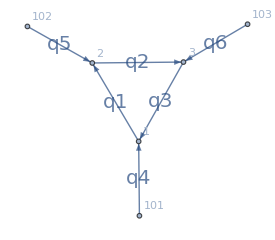

```mathematica
Tri1L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],DirectedEdge[3,1,3],
DirectedEdge[101,1,4],DirectedEdge[102,2,5],DirectedEdge[103,3,6]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Tri1L=AssignSignatures[Tri1L,masses-><|1->1,2->2,3->3|>,lmb->{1}];
Tri1L=DirectedGraph[Tri1L,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]),FontSize->20],{e,EdgeList[Tri1L]}]]
```

```mathematica
Tri1Lnumerics=GenerateRandomSample[Tri1L,Seed->1]
```

{k1→{2/3,3/5,5/7},p1→{7/11,11/13,13/17},p2→{17/19,19/23,23/29},p1E→29/31,p2E→31/37,p3→{-320/209,-500/299,-768/493},p3E→-2034/1147}

```mathematica
GenerateLMBData[g_]:=Module[
{
edges=EdgeList[g],
props,
lmbEdgesIDs=Table[(e/.DirectedEdge[_,_,props_]:>props)["id"],{e,cFFGetLMBEdges[g]}],
externals=cFFGetExternalEdges[g]
},
Association[Table[
props=(e/.DirectedEdge[_,_,props_]:>props);
props["id"]-><|
"mass"->props["mass"],
"lmb_decomposition"->(
props["sig"]⟦1⟧.Table[q[i],{i,Length[lmbEdgesIDs]}]
+props["sig"]⟦2⟧.Table[q[i+3],{i,Length[externals]}]
)
|>
,{e,edges}
]]
]
```

```mathematica
GetVirtualPropagators[g_]:=Module[
{
externalIDs=Table[(e/.DirectedEdge[_,_,props_]:>props)["id"],{e,cFFGetExternalEdges[g]}]
},
Select[EdgeList[g],Not[MemberQ[externalIDs,(#/.DirectedEdge[_,_,props_]:>props)["id"]]]&]
]
```

```mathematica
GetVirtualPropagatorsIDs[g_]:=Table[(e/.DirectedEdge[_,_,props_]:>props)["id"],{e,GetVirtualPropagators[g]}]
```

```mathematica
ExpandSP4[Num_]:=TensorExpand[Num/.{SP4[a_,b_]:>Cross[a/.{v_[i_]:>L[v[i]]},b/.{v_[i_]:>R[v[i]]}]}]/.{Cross[L[a_],R[b_]]:>SP4[a,b]};
```

```mathematica
Tri1Lnumerator=SP4[q[1],q[2]]SP4[q[3],q[4]]+SP4[q[1],q[3]]SP4[q[2],q[5]]+SP4[q[1],q[2]]+SP4[q[1],q[3]]+1 ;
```

```mathematica
(*Tri1Lnumerator=SP4[q[1],q[2]]SP4[q[3],q[4]];*)
```

```mathematica
(*Tri1Lnumerator=SP4[q[1],q[3]]SP4[q[2],q[5]];*)
```

```mathematica
(*Tri1Lnumerator=SP4[q[1],q[2]];*)
```

```mathematica
Tri1LcLTDexpr=GeneratecLTDExpression[Tri1L,Num->Tri1Lnumerator];
Print["cLTD result: ",EvalcLTD[Tri1LcLTDexpr,Tri1Lnumerics]//N//FullForm];
Tri1LcFFexpr=CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True];
Print["cFF result : ",EvalcFF[Tri1L,Tri1LcFFexpr,Tri1Lnumerics,Num->Tri1Lnumerator,DEBUG->False]//N//FullForm];
```

cLTD result: Complex[0.,0.00471006]

cFF result : Complex[0.,0.00471006]

```mathematica
Tri1LPropagators=GenerateLMBData[Tri1L];
```

```mathematica
Tri1L4DExpr=Num[Tri1Lnumerator]/Times@@Table[1/λ^2 Denom[ie,SP4[q[ie][λ],q[ie][λ]]-λ^2 m[ie]^2+(m[ie]^2-mUV^2)],{ie,GetVirtualPropagatorsIDs[Tri1L]}]
```

(λ^6 Num[1+SP4[q[1],q[2]]+SP4[q[1],q[3]]+SP4[q[1],q[3]] SP4[q[2],q[5]]+SP4[q[1],q[2]] SP4[q[3],q[4]]])/(Denom[1,-mUV^2+m[1]^2-λ^2 m[1]^2+SP4[q[1][λ],q[1][λ]]] Denom[2,-mUV^2+m[2]^2-λ^2 m[2]^2+SP4[q[2][λ],q[2][λ]]] Denom[3,-mUV^2+m[3]^2-λ^2 m[3]^2+SP4[q[3][λ],q[3][λ]]])

```mathematica
Tri1L4DExprWithFullLambdaDep=Collect[(1/λ)^4 Tri1L4DExpr/.
{
Num[x__]:>(x
/.
Table[q[ie]->1/λ q[ie][λ],{ie,GetVirtualPropagatorsIDs[Tri1L]}]
/.{
SP4[1/λ a_,1/λ b_]:>1/λ^2 SP4[a,b]
}/.
{SP4[1/λ a_,b_]:>1/λ SP4[a,b]}
)
},λ]
```

λ^2/(Denom[1,-mUV^2+m[1]^2-λ^2 m[1]^2+SP4[q[1][λ],q[1][λ]]] Denom[2,-mUV^2+m[2]^2-λ^2 m[2]^2+SP4[q[2][λ],q[2][λ]]] Denom[3,-mUV^2+m[3]^2-λ^2 m[3]^2+SP4[q[3][λ],q[3][λ]]])+(SP4[q[1][λ],q[2][λ]]+SP4[q[1][λ],q[3][λ]])/(Denom[1,-mUV^2+m[1]^2-λ^2 m[1]^2+SP4[q[1][λ],q[1][λ]]] Denom[2,-mUV^2+m[2]^2-λ^2 m[2]^2+SP4[q[2][λ],q[2][λ]]] Denom[3,-mUV^2+m[3]^2-λ^2 m[3]^2+SP4[q[3][λ],q[3][λ]]])+(SP4[q[4],q[3][λ]] SP4[q[1][λ],q[2][λ]]+SP4[q[5],q[2][λ]] SP4[q[1][λ],q[3][λ]])/(λ Denom[1,-mUV^2+m[1]^2-λ^2 m[1]^2+SP4[q[1][λ],q[1][λ]]] Denom[2,-mUV^2+m[2]^2-λ^2 m[2]^2+SP4[q[2][λ],q[2][λ]]] Denom[3,-mUV^2+m[3]^2-λ^2 m[3]^2+SP4[q[3][λ],q[3][λ]]])

```mathematica
Tri1L4DExprWithFullLambdaDepDODsplits=Association[Table[pwr->λ^pwr Coefficient[Tri1L4DExprWithFullLambdaDep,λ^pwr],{pwr,{-1,1,2}}]]
```

<|-1→(SP4[q[4],q[3][λ]] SP4[q[1][λ],q[2][λ]]+SP4[q[5],q[2][λ]] SP4[q[1][λ],q[3][λ]])/(λ Denom[1,-mUV^2+m[1]^2-λ^2 m[1]^2+SP4[q[1][λ],q[1][λ]]] Denom[2,-mUV^2+m[2]^2-λ^2 m[2]^2+SP4[q[2][λ],q[2][λ]]] Denom[3,-mUV^2+m[3]^2-λ^2 m[3]^2+SP4[q[3][λ],q[3][λ]]]),1→0,2→λ^2/(Denom[1,-mUV^2+m[1]^2-λ^2 m[1]^2+SP4[q[1][λ],q[1][λ]]] Denom[2,-mUV^2+m[2]^2-λ^2 m[2]^2+SP4[q[2][λ],q[2][λ]]] Denom[3,-mUV^2+m[3]^2-λ^2 m[3]^2+SP4[q[3][λ],q[3][λ]]])|>

```mathematica
AssociateTo[Tri1L4DExprWithFullLambdaDepDODsplits,0->Tri1L4DExprWithFullLambdaDep-Total[Values[Tri1L4DExprWithFullLambdaDepDODsplits]]];
```

```mathematica
SeriesCoefficient[Series[Tri1L4DExprWithFullLambdaDepDODsplits[-1],{λ,0,0}],-1]/.{Denom[___]:>1}/.{q[a_][0]:>q[a]}
```

SP4[q[1],q[3]] SP4[q[2],q[5]]+SP4[q[1],q[2]] SP4[q[3],q[4]]

```mathematica
Tri1LUVTopologies=<||>;
```

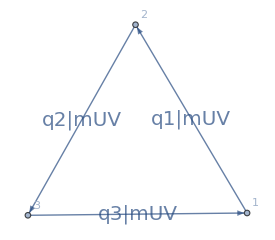
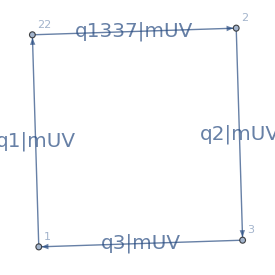
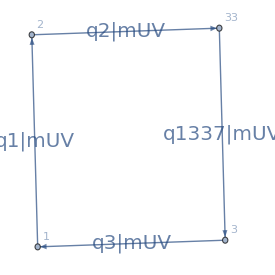
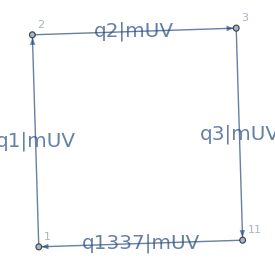
<|{}→-Graphics-,{1}→-Graphics-,{2}→-Graphics-,{3}→-Graphics-|>

```mathematica
Tri1LUVTopology=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],DirectedEdge[3,1,3]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Tri1LUVTopology=AssignSignatures[Tri1LUVTopology,masses-><|1->mUV,2->mUV,3->mUV|>,lmb->{1}];
Tri1LUVTopology=DirectedGraph[Tri1LUVTopology,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]<>"|"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["mass"])]),FontSize->20],{e,EdgeList[Tri1LUVTopology]}]];
AssociateTo[Tri1LUVTopologies,{}->Tri1LUVTopology];
Tri1LUVTopology=DirectedGraph[{
DirectedEdge[1,22,1],DirectedEdge[2,3,2],DirectedEdge[3,1,3],DirectedEdge[22,2,1337]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Tri1LUVTopology=AssignSignatures[Tri1LUVTopology,masses-><|1->mUV,2->mUV,3->mUV,1337->mUV|>,lmb->{1}];
Tri1LUVTopology=DirectedGraph[Tri1LUVTopology,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]<>"|"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["mass"])]),FontSize->20],{e,EdgeList[Tri1LUVTopology]}]];
AssociateTo[Tri1LUVTopologies,{1}->Tri1LUVTopology];
Tri1LUVTopology=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,33,2],DirectedEdge[3,1,3],DirectedEdge[33,3,1337]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Tri1LUVTopology=AssignSignatures[Tri1LUVTopology,masses-><|1->mUV,2->mUV,3->mUV,1337->mUV|>,lmb->{1}];
Tri1LUVTopology=DirectedGraph[Tri1LUVTopology,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]<>"|"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["mass"])]),FontSize->20],{e,EdgeList[Tri1LUVTopology]}]];
AssociateTo[Tri1LUVTopologies,{2}->Tri1LUVTopology];
Tri1LUVTopology=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],DirectedEdge[3,11,3],DirectedEdge[11,1,1337]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Tri1LUVTopology=AssignSignatures[Tri1LUVTopology,masses-><|1->mUV,2->mUV,3->mUV,1337->mUV|>,lmb->{1}];
Tri1LUVTopology=DirectedGraph[Tri1LUVTopology,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]<>"|"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["mass"])]),FontSize->20],{e,EdgeList[Tri1LUVTopology]}]];
AssociateTo[Tri1LUVTopologies,{3}->Tri1LUVTopology]
```

```mathematica
SubtractionData=<|
"I"-><|
"cFFexpr"->CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],
"num"->Tri1Lnumerator,
"graph"->Tri1L
|>,
-1-><|
-1-><||>,0-><||>
|>,
0-><|
0-><||>
|>
|>;
```

```mathematica
ComputeSubtractionTerm[ct_,numerics_]:=Module[{orkey,sortedEdgeIDs},
sortedEdgeIDs=Sort[Table[(e/.{DirectedEdge[_,_,props_]:>props})["id"],{e,GetVirtualPropagators[ct["graph"]]}]];
Association[SortBy[Table[
orkey=Table[
orientation["Orientation"][eID],
{eID,sortedEdgeIDs}
];
orkey->
(1/λ)^3 EvalcFF[
ct["graph"],
{orientation},
numerics/.{Rule[k1,a_]->Rule[k1,1/λ a]},
Num->ct["num"],
DEBUG->False]
,
{orientation,ct["cFFexpr"]}],(#⟦1⟧)&]
]]
```

```mathematica
subtractionNumerics=Join[
Tri1Lnumerics,
{mUV->1,
p[1][0]->(p1E/.Tri1Lnumerics),p[2][0]->(p2E/.Tri1Lnumerics),p[3][0]->(p3E/.Tri1Lnumerics),
p[1]->(p1/.Tri1Lnumerics),p[2]->(p2/.Tri1Lnumerics),p[3]->(p3/.Tri1Lnumerics)
}];
```

```mathematica
IRes=ComputeSubtractionTerm[SubtractionData["I"],Tri1Lnumerics];
```

```mathematica
lmbVec=q[cFFGetLMBEdges[Tri1L]⟦1⟧/.{DirectedEdge[_,_,props_]:>props["id"]}];
```

```mathematica
lmbData=GenerateLMBData[Tri1L];
lmbDataLambda=Association[Table[k-><|
"mass"->λ lmbData[k]["mass"],"lmb_decomposition"->Simplify[λ (lmbData[k]["lmb_decomposition"]/.{lmbVec->1/λ lmbVec})]|>,
{k,Keys[lmbData]}]]
```

<|1→<|mass→λ,lmb_decomposition→q[1]|>,2→<|mass→2 λ,lmb_decomposition→q[1]-λ (q[4]+q[6])|>,3→<|mass→3 λ,lmb_decomposition→q[1]-λ q[4]|>,4→<|mass→0,lmb_decomposition→λ q[4]|>,5→<|mass→0,lmb_decomposition→λ q[5]|>,6→<|mass→0,lmb_decomposition→λ q[6]|>|>

### dod -1 term

```mathematica
AssociateTo[SubtractionData[-1][-1],{}-><|
"cFFexpr"->CrossFreeFamilyLTD[Tri1LUVTopologies[{}],ConvertToNormalisedFormat->True],
"num"-> SeriesCoefficient[Series[Tri1L4DExprWithFullLambdaDepDODsplits[-1],{λ,0,0}],-1]/.{Denom[___]:>1}/.{q[a_][0]:>q[a]}/.{q[4]->p[1],q[5]->p[2],q[6]->(-p[1]-p[2])},
"graph"->Tri1LUVTopologies[{}]
|>];
```

```mathematica
dodm1Res=ComputeSubtractionTerm[SubtractionData[-1][-1][{}],subtractionNumerics];
```

```mathematica
Module[
{tmpI,tmpCT},
Table[
tmpI=SeriesCoefficient[Series[IRes[o],{λ,0,-1},Assumptions->λ>0],-1];
tmpCT=SeriesCoefficient[Series[dodm1Res[o],{λ,0,-1},Assumptions->λ>0],-1];
{o,tmpI,tmpCT,FullSimplify[tmpI-tmpCT]}
,{o,Keys[IRes]}]
]//N//MatrixForm
```

({-1.,-1.,1.} | 0.+0.108605 ⅈ | 0.+0.108605 ⅈ | 0.
{-1.,1.,-1.} | 0.+0.105763 ⅈ | 0.+0.105763 ⅈ | 0.
{-1.,1.,1.} | 0.+0.0457567 ⅈ | 0.+0.0457567 ⅈ | 0.
{1.,-1.,-1.} | 0.+0.214368 ⅈ | 0.+0.214368 ⅈ | 0.
{1.,-1.,1.} | 0.+0.0168153 ⅈ | 0.+0.0168153 ⅈ | 0.
{1.,1.,-1.} | 0.+0.0289414 ⅈ | 0.+0.0289414 ⅈ | 0.)

### dod 0 term

```mathematica
dod0Expr=SeriesCoefficient[Series[Tri1L4DExprWithFullLambdaDepDODsplits[-1]+Tri1L4DExprWithFullLambdaDepDODsplits[0],{λ,0,0}],0]//Expand;
```

Now split the above expression into its various denominator structures

```mathematica
dod0NumNoDot=<|
{}->ExpandSP4[(dod0Expr/.{x__*Denom[id_,y__]^-2:>0}/.{Denom[y__]:>1})/.{
x__*Derivative[1][q[ie_]][0]Derivative[0,1][SP4][a_,b_]:>x SP4[a,D[lmbDataLambda[ie]["lmb_decomposition"],λ]],
x__*Derivative[1][q[ie_]][0]Derivative[1,0][SP4][a_,b_]:>x SP4[D[lmbDataLambda[ie]["lmb_decomposition"],λ],b]
}/.SP4[0,x__]:>0
/.{q[ie_][0]->q[ie]}]
|>
```

<|{}→SP4[q[1],q[2]]+SP4[q[1],q[3]]-SP4[q[1],q[4]] SP4[q[2],q[5]]-SP4[q[1],q[4]] SP4[q[3],q[4]]-SP4[q[1],q[6]] SP4[q[3],q[4]]-SP4[q[1],q[2]] SP4[q[4],q[4]]-SP4[q[1],q[3]] SP4[q[4],q[5]]-SP4[q[1],q[3]] SP4[q[5],q[6]]|>

```mathematica
dod0NumNoDot[{}]
```

SP4[q[1],q[2]]+SP4[q[1],q[3]]-SP4[q[1],q[4]] SP4[q[2],q[5]]-SP4[q[1],q[4]] SP4[q[3],q[4]]-SP4[q[1],q[6]] SP4[q[3],q[4]]-SP4[q[1],q[2]] SP4[q[4],q[4]]-SP4[q[1],q[3]] SP4[q[4],q[5]]-SP4[q[1],q[3]] SP4[q[5],q[6]]

```mathematica
AssociateTo[SubtractionData[0][0],{}-><|
"cFFexpr"->CrossFreeFamilyLTD[Tri1LUVTopologies[{}],ConvertToNormalisedFormat->True],
"num"-> dod0NumNoDot[{}]/.{q[a_][0]:>q[a]}/.{q[4]->p[1],q[5]->p[2],q[6]->(-p[1]-p[2])},
"graph"->Tri1LUVTopologies[{}]
|>];
```

Now select each dotted topology separately

```mathematica
dod0NumDotted=Association[Table[
{{dot}->(
ExpandSP4[dod0Expr
/.{x__*Power[Denom[idA_,__],-1]*Power[Denom[idB_,__],-1]*Power[Denom[idC_,__],-1]:>0}
/.{x__*Power[Denom[idA_,__],-1]*Power[Denom[idB_,__],-1]*Power[Denom[idC_?(!(#===dot)&),__],-2]:>0}
/.{Denom[y__]:>1}
/.x__ Derivative[1][q[dot]][0]Derivative[0,1][SP4][q[dot][0],q[dot][0]]Derivative[0,1][Denom][dot,z___]:>x SP4[q[1337],D[lmbDataLambda[dot]["lmb_decomposition"],λ]]
/.x__ Derivative[1][q[dot]][0]Derivative[1,0][SP4][q[dot][0],q[dot][0]]Derivative[0,1][Denom][dot,z___]:>x SP4[q[1337],D[lmbDataLambda[dot]["lmb_decomposition"],λ]]
/.SP4[0,x__]:>0
/.{q[ie_][0]->q[ie]}
]
)},
{dot,{1,2,3}}
]]
```

<|{1}→0,{2}→2 SP4[q[1],q[3]] SP4[q[2],q[5]] SP4[q[4],q[1337]]+2 SP4[q[1],q[2]] SP4[q[3],q[4]] SP4[q[4],q[1337]]+2 SP4[q[1],q[3]] SP4[q[2],q[5]] SP4[q[6],q[1337]]+2 SP4[q[1],q[2]] SP4[q[3],q[4]] SP4[q[6],q[1337]],{3}→2 SP4[q[1],q[3]] SP4[q[2],q[5]] SP4[q[4],q[1337]]+2 SP4[q[1],q[2]] SP4[q[3],q[4]] SP4[q[4],q[1337]]|>

```mathematica
Table[
(*If[!(dod0NumDotted[d]===0),*)
AssociateTo[SubtractionData[0][0],d-><|
"cFFexpr"->CrossFreeFamilyLTD[Tri1LUVTopologies[d],ConvertToNormalisedFormat->True],
"num"-> dod0NumDotted[d]/.{q[a_][0]:>q[a]}/.{q[4]->p[1],q[5]->p[2],q[6]->(-p[1]-p[2])},
"graph"->Tri1LUVTopologies[d]
|>];
(*];*)
,{d,Keys[dod0NumDotted]}];
```

```mathematica
IRes=ComputeSubtractionTerm[SubtractionData["I"],Tri1Lnumerics];
```

```mathematica
dodm0NotDotRes=ComputeSubtractionTerm[SubtractionData[0][0][{}],subtractionNumerics];
```

```mathematica
dodm0DottedRes={
ComputeSubtractionTerm[SubtractionData[0][0][{1}],subtractionNumerics],
ComputeSubtractionTerm[SubtractionData[0][0][{2}],subtractionNumerics],
ComputeSubtractionTerm[SubtractionData[0][0][{3}],subtractionNumerics]
};
```

```mathematica
Module[
{tmpI,tmpCTnoDot,
tmpCTDot1Minus,tmpCTDot2Minus,tmpCTDot3Minus,
tmpCTDot1Plus,tmpCTDot2Plus,tmpCTDot3Plus,
,res,minusKey,plusKey},
res=Table[
tmpI=SeriesCoefficient[Series[IRes[o],{λ,0,0},Assumptions->λ>0],0]/.{Missing[x__]:>0};
tmpCTnoDot=SeriesCoefficient[Series[dodm0NotDotRes[o],{λ,0,0},Assumptions->λ>0],0]/.{Missing[x__]:>0};
minusKey=Join[o,{-1}];
tmpCTDot1Minus=SeriesCoefficient[Series[dodm0DottedRes⟦1⟧[minusKey],{λ,0,0},Assumptions->λ>0],0]/.{Missing[x__]:>0};
tmpCTDot2Minus=SeriesCoefficient[Series[dodm0DottedRes⟦2⟧[minusKey],{λ,0,0},Assumptions->λ>0],0]/.{Missing[x__]:>0};
tmpCTDot3Minus=SeriesCoefficient[Series[dodm0DottedRes⟦3⟧[minusKey],{λ,0,0},Assumptions->λ>0],0]/.{Missing[x__]:>0};
plusKey=Join[o,{1}];
tmpCTDot1Plus=SeriesCoefficient[Series[dodm0DottedRes⟦1⟧[plusKey],{λ,0,0},Assumptions->λ>0],0]/.{Missing[x__]:>0};
tmpCTDot2Plus=SeriesCoefficient[Series[dodm0DottedRes⟦2⟧[plusKey],{λ,0,0},Assumptions->λ>0],0]/.{Missing[x__]:>0};
tmpCTDot3Plus=SeriesCoefficient[Series[dodm0DottedRes⟦3⟧[plusKey],{λ,0,0},Assumptions->λ>0],0]/.{Missing[x__]:>0};
{o,
tmpI,
(-tmpCTnoDot-tmpCTDot1Minus-tmpCTDot2Minus-tmpCTDot3Minus-tmpCTDot1Plus-tmpCTDot2Plus-tmpCTDot3Plus),
FullSimplify[tmpI-tmpCTnoDot-tmpCTDot1Minus-tmpCTDot2Minus-tmpCTDot3Minus-tmpCTDot1Plus-tmpCTDot2Plus-tmpCTDot3Plus],
tmpCTnoDot,
tmpCTDot1Minus,tmpCTDot1Plus,tmpCTDot2Minus,tmpCTDot2Plus,tmpCTDot3Minus,tmpCTDot3Plus
}
,{o,Keys[IRes]}
];
res=Join[{{
"orientation","I","-SumCT","I-SumCT","CTNoDot","CTDot1-","CTDot1+","CTDot2-","CTDot2+","CTDot3-","CTDot3+"
}},res];
AppendTo[res,Join[{"TOTAL"},
N[Table[
Total[Table[r⟦ri⟧,{r,res⟦2;;⟧}]],
{ri,2,Length[res⟦1⟧]}
]]
]]
]//N//MatrixForm
```

(orientation | I | -SumCT | I-SumCT | CTNoDot | CTDot1- | CTDot1+ | CTDot2- | CTDot2+ | CTDot3- | CTDot3+
{-1.,-1.,1.} | 0.-0.115351 ⅈ | 0.+0.0985998 ⅈ | 0.-0.0167513 ⅈ | 0.-0.0716091 ⅈ | 0. | 0. | 0.-0.108192 ⅈ | 0.-0.0576625 ⅈ | 0.+0.105361 ⅈ | 0.+0.0335027 ⅈ
{-1.,1.,-1.} | 0.+0.0031744 ⅈ | 0.+0.0249025 ⅈ | 0.+0.0280769 ⅈ | 0.+0.00138199 ⅈ | 0. | 0. | 0.-0.105361 ⅈ | 0.-0.0561538 ⅈ | 0.+0.102604 ⅈ | 0.+0.0326261 ⅈ
{-1.,1.,1.} | 0.-0.0890274 ⅈ | 0.+0.0777019 ⅈ | 0.-0.0113256 ⅈ | 0.-0.0702271 ⅈ | 0. | 0. | 0.-0.0911652 ⅈ | 0.-0.012147 ⅈ | 0.+0.0887799 ⅈ | 0.+0.00705754 ⅈ
{1.,-1.,-1.} | 0.-0.0895256 ⅈ | 0.+0.100851 ⅈ | 0.+0.0113256 ⅈ | 0.-0.047576 ⅈ | 0. | 0. | 0.-0.213553 ⅈ | 0.-0.113816 ⅈ | 0.+0.207965 ⅈ | 0.+0.0661287 ⅈ
{1.,-1.,1.} | 0.-0.0741852 ⅈ | 0.+0.0909365 ⅈ | 0.+0.0167513 ⅈ | 0.-0.0881896 ⅈ | 0. | 0. | 0.-0.0335027 ⅈ | 0.-0.00446394 ⅈ | 0.+0.0326261 ⅈ | 0.+0.00259361 ⅈ
{1.,1.,-1.} | 0.+0.00780885 ⅈ | 0.-0.0358858 ⅈ | 0.-0.0280769 ⅈ | 0.+0.0406136 ⅈ | 0. | 0. | 0.-0.0576625 ⅈ | 0.-0.00768303 ⅈ | 0.+0.0561538 ⅈ | 0.+0.00446394 ⅈ
TOTAL | 0.-0.357106 ⅈ | 0.+0.357106 ⅈ | 0. | 0.-0.235606 ⅈ | 0. | 0. | 0.-0.609436 ⅈ | 0.-0.251927 ⅈ | 0.+0.59349 ⅈ | 0.+0.146373 ⅈ)

### dod 0 term with derivatives for dotted topologies

```mathematica
dod0Expr=SeriesCoefficient[Series[Tri1L4DExprWithFullLambdaDepDODsplits[-1]+Tri1L4DExprWithFullLambdaDepDODsplits[0],{λ,0,0}],0]//Expand;
```

Now split the above expression into its various denominator structures

```mathematica
dod0NumNoDot=<|
{}->ExpandSP4[(dod0Expr/.{x__*Denom[id_,y__]^-2:>0}/.{Denom[y__]:>1})/.{
x__*Derivative[1][q[ie_]][0]Derivative[0,1][SP4][a_,b_]:>x SP4[a,D[lmbDataLambda[ie]["lmb_decomposition"],λ]],
x__*Derivative[1][q[ie_]][0]Derivative[1,0][SP4][a_,b_]:>x SP4[D[lmbDataLambda[ie]["lmb_decomposition"],λ],b]
}/.SP4[0,x__]:>0
/.{q[ie_][0]->q[ie]}]
|>
```

<|{}→SP4[q[1],q[2]]+SP4[q[1],q[3]]-SP4[q[1],q[4]] SP4[q[2],q[5]]-SP4[q[1],q[4]] SP4[q[3],q[4]]-SP4[q[1],q[6]] SP4[q[3],q[4]]-SP4[q[1],q[2]] SP4[q[4],q[4]]-SP4[q[1],q[3]] SP4[q[4],q[5]]-SP4[q[1],q[3]] SP4[q[5],q[6]]|>

```mathematica
dod0NumNoDot[{}]
```

SP4[q[1],q[2]]+SP4[q[1],q[3]]-SP4[q[1],q[4]] SP4[q[2],q[5]]-SP4[q[1],q[4]] SP4[q[3],q[4]]-SP4[q[1],q[6]] SP4[q[3],q[4]]-SP4[q[1],q[2]] SP4[q[4],q[4]]-SP4[q[1],q[3]] SP4[q[4],q[5]]-SP4[q[1],q[3]] SP4[q[5],q[6]]

```mathematica
SubtractionContribs=<||>;
```

```mathematica
AssociateTo[SubtractionContribs,"NumExpansion"->{<|
"cFFexpr"->CrossFreeFamilyLTD[Tri1LUVTopologies[{}],ConvertToNormalisedFormat->True],
"num"-> dod0NumNoDot[{}]/.{SP4[q[a_],q[b_]]:>qE[a]*qE[b]-q[a].q[b]}(*/.{q[a_][0]:>q[a]}/.{q[4]->p[1],q[5]->p[2],q[6]->(-p[1]-p[2])}*),
"graph"->Tri1LUVTopologies[{}]
|>}];
```

Now select each dotted topology separately

```mathematica
dod0NumDotted=Association[Table[
{{dot}->(
ExpandSP4[dod0Expr
/.{x__*Power[Denom[idA_,__],-1]*Power[Denom[idB_,__],-1]*Power[Denom[idC_,__],-1]:>0}
/.{x__*Power[Denom[idA_,__],-1]*Power[Denom[idB_,__],-1]*Power[Denom[idC_?(!(#===dot)&),__],-2]:>0}
/.{Denom[y__]:>1}
/.x__ Derivative[1][q[dot]][0]Derivative[0,1][SP4][q[dot][0],q[dot][0]]Derivative[0,1][Denom][dot,z___]:>x SP4[q[dot],D[lmbDataLambda[dot]["lmb_decomposition"],λ]]
/.x__ Derivative[1][q[dot]][0]Derivative[1,0][SP4][q[dot][0],q[dot][0]]Derivative[0,1][Denom][dot,z___]:>x SP4[q[dot],D[lmbDataLambda[dot]["lmb_decomposition"],λ]]
/.SP4[0,x__]:>0
/.{q[ie_][0]->q[ie]}
]
)},
{dot,{1,2,3}}
]]
```

<|{1}→0,{2}→2 SP4[q[1],q[3]] SP4[q[2],q[4]] SP4[q[2],q[5]]+2 SP4[q[1],q[3]] SP4[q[2],q[5]] SP4[q[2],q[6]]+2 SP4[q[1],q[2]] SP4[q[2],q[4]] SP4[q[3],q[4]]+2 SP4[q[1],q[2]] SP4[q[2],q[6]] SP4[q[3],q[4]],{3}→2 SP4[q[1],q[3]] SP4[q[2],q[5]] SP4[q[3],q[4]]+2 SP4[q[1],q[2]] SP4[q[3],q[4]]^2|>

We will use the following identity to compute the CFF expression of the dotted topologies

∫dk^0(N(q^0,q⃗))/D^α=1/Γ[α](1/(2 E(q⃗)))^(α-1)(∂/(∂ E(q⃗)))^(α-1)∫dk^0(N(q^0,q⃗))/D=1/Γ[α](1/(2 E(q⃗)))^(α-1)(∂/(∂ E(q⃗)))^(α-1)∑_(σ⃗) N_(σ⃗)(E(q⃗),q⃗)CFF_(σ⃗)(E(q⃗))

It will then useful to write the numerator in the EMR as a polynomial over energies q_i^0

```mathematica
MaxqOPower=3;
```

```mathematica
Tri1LNumCoefs=Table[
CoefficientList[TensorExpand[dod0NumDotted[{ie}]/.{SP4[q[a_],q[b_]]:>qE[a]*qE[b]-q[a].q[b]}],{qE[1],qE[2],qE[3]},{MaxqOPower,MaxqOPower,MaxqOPower}]//Flatten,
{ie,{1,2,3}}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-2 q[1].q[3] q[2].q[4] q[2].q[5]-2 q[1].q[3] q[2].q[5] q[2].q[6]-2 q[1].q[2] q[2].q[4] q[3].q[4]-2 q[1].q[2] q[2].q[6] q[3].q[4],2 q[1].q[2] q[2].q[4] qE[4]+2 q[1].q[2] q[2].q[6] qE[4],0,2 q[1].q[3] q[2].q[5] qE[4]+2 q[1].q[2] q[3].q[4] qE[4]+2 q[1].q[3] q[2].q[4] qE[5]+2 q[1].q[3] q[2].q[6] qE[5]+2 q[1].q[3] q[2].q[5] qE[6]+2 q[1].q[2] q[3].q[4] qE[6],-2 q[1].q[2] qE[4]^2-2 q[1].q[2] qE[4] qE[6],0,-2 q[1].q[3] qE[4] qE[5]-2 q[1].q[3] qE[5] qE[6],0,0,0,2 q[2].q[4] q[2].q[5]+2 q[2].q[5] q[2].q[6],0,2 q[2].q[4] q[3].q[4]+2 q[2].q[6] q[3].q[4],-2 q[2].q[4] qE[4]-2 q[2].q[5] qE[4]-2 q[2].q[6] qE[4]-2 q[2].q[4] qE[5]-2 q[2].q[6] qE[5]-2 q[2].q[5] qE[6],0,-2 q[3].q[4] qE[4]-2 q[3].q[4] qE[6],2 qE[4]^2+2 qE[4] qE[5]+2 qE[4] qE[6]+2 qE[5] qE[6],0,0,0,0,0,0,0,0,0,0},{-2 q[1].q[3] q[2].q[5] q[3].q[4]-2 q[1].q[2] (q[3].q[4])^2,2 q[1].q[3] q[2].q[5] qE[4]+4 q[1].q[2] q[3].q[4] qE[4],-2 q[1].q[2] qE[4]^2,2 q[1].q[3] q[3].q[4] qE[5],-2 q[1].q[3] qE[4] qE[5],0,0,0,0,0,2 q[2].q[5] q[3].q[4],-2 q[2].q[5] qE[4],2 (q[3].q[4])^2,-4 q[3].q[4] qE[4]-2 q[3].q[4] qE[5],2 qE[4]^2+2 qE[4] qE[5],0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Tri1LNumOSEVars=CoefficientList[Expand[(1+qE[1]OSE[1]+qE[1]^2 OSE[1]^2)(1+qE[2]OSE[2]+qE[2]^2 OSE[2]^2)(1+qE[3]OSE[3]+qE[3]^2 OSE[3]^2)],{qE[1],qE[2],qE[3]},{MaxqOPower,MaxqOPower,MaxqOPower}]//Flatten
```

{1,OSE[3],OSE[3]^2,OSE[2],OSE[2] OSE[3],OSE[2] OSE[3]^2,OSE[2]^2,OSE[2]^2 OSE[3],OSE[2]^2 OSE[3]^2,OSE[1],OSE[1] OSE[3],OSE[1] OSE[3]^2,OSE[1] OSE[2],OSE[1] OSE[2] OSE[3],OSE[1] OSE[2] OSE[3]^2,OSE[1] OSE[2]^2,OSE[1] OSE[2]^2 OSE[3],OSE[1] OSE[2]^2 OSE[3]^2,OSE[1]^2,OSE[1]^2 OSE[3],OSE[1]^2 OSE[3]^2,OSE[1]^2 OSE[2],OSE[1]^2 OSE[2] OSE[3],OSE[1]^2 OSE[2] OSE[3]^2,OSE[1]^2 OSE[2]^2,OSE[1]^2 OSE[2]^2 OSE[3],OSE[1]^2 OSE[2]^2 OSE[3]^2}

```mathematica
Tri1LNumVars=Tri1LNumOSEVars/.{OSE[i_]:>qE[i]};
```

```mathematica
Table[

If[Not[
Simplify[TensorExpand[dod0NumDotted[{ie}]/.{SP4[q[a_],q[b_]]:>qE[a]*qE[b]-q[a].q[b]}/.{qE[1]->OSE[1],qE[2]->OSE[2],qE[3]->OSE[3]}]-Tri1LNumCoefs⟦ie⟧.Tri1LNumOSEVars]===0
],Print["HIGHER POWER NUMERATORS MUST BE HANDLED BEFOREHAND WITH q0^2= q^2+OSE[q]^2 for dot #"<>ToString[ie]],Print["Numerator check passed for dot #"<>ToString[ie]]],

{ie,{1,2,3}}
];
```

Numerator check passed for dot #1

Numerator check passed for dot #2

Numerator check passed for dot #3

For a given dotted topology, there are 2 types of derivatives to consider:

a) Numerator derivatives in the OSE variable corresponding to the dot (NumDOSEDot<i=1,2,3>)
b) Derivatives of CFF in the OSE variable corresponding to the dot (CFFDOSEDot<i=1,2,3>)

a) NumDOSEDot<i=1,2,3>

```mathematica
Tri1LNumVarsDOSEDot=Table[
D[Tri1LNumVars,{qE[dot]}],
{dot,{1,2,3}}
]
```

{{0,0,0,0,0,0,0,0,0,1,qE[3],qE[3]^2,qE[2],qE[2] qE[3],qE[2] qE[3]^2,qE[2]^2,qE[2]^2 qE[3],qE[2]^2 qE[3]^2,2 qE[1],2 qE[1] qE[3],2 qE[1] qE[3]^2,2 qE[1] qE[2],2 qE[1] qE[2] qE[3],2 qE[1] qE[2] qE[3]^2,2 qE[1] qE[2]^2,2 qE[1] qE[2]^2 qE[3],2 qE[1] qE[2]^2 qE[3]^2},{0,0,0,1,qE[3],qE[3]^2,2 qE[2],2 qE[2] qE[3],2 qE[2] qE[3]^2,0,0,0,qE[1],qE[1] qE[3],qE[1] qE[3]^2,2 qE[1] qE[2],2 qE[1] qE[2] qE[3],2 qE[1] qE[2] qE[3]^2,0,0,0,qE[1]^2,qE[1]^2 qE[3],qE[1]^2 qE[3]^2,2 qE[1]^2 qE[2],2 qE[1]^2 qE[2] qE[3],2 qE[1]^2 qE[2] qE[3]^2},{0,1,2 qE[3],0,qE[2],2 qE[2] qE[3],0,qE[2]^2,2 qE[2]^2 qE[3],0,qE[1],2 qE[1] qE[3],0,qE[1] qE[2],2 qE[1] qE[2] qE[3],0,qE[1] qE[2]^2,2 qE[1] qE[2]^2 qE[3],0,qE[1]^2,2 qE[1]^2 qE[3],0,qE[1]^2 qE[2],2 qE[1]^2 qE[2] qE[3],0,qE[1]^2 qE[2]^2,2 qE[1]^2 qE[2]^2 qE[3]}}

```mathematica
Tri1LCFFNumDOSEDot=Block[
{newTerms,foundIt,esurfs},
Table[
Table[
(*Do not forget to capture the orientation sign stemming form the numerator OSE derivative *)
newTerms=Table[
esurfs=Join[es["Esurfs"],{<|"overall_sign"->o["Orientation"][id],"OSE"->{id},"shift_signature"->{}|>}];
<|
"Num"->1/2,
"Orderings"->Null,
"Esurfs"->esurfs
|>,{es,o["Terms"]}];

<|"Orientation"->o["Orientation"],"Terms"->newTerms|>

,{o,CrossFreeFamilyLTD[Tri1LUVTopologies[{}],ConvertToNormalisedFormat->True]}
]
,{id,{1,2,3}}]
];
```

```mathematica
AssociateTo[SubtractionContribs,"NumDOSEDot"->Table[
<|
"cFFexpr"->Tri1LCFFNumDOSEDot⟦ie⟧,
"num"->Tri1LNumCoefs⟦ie⟧.Tri1LNumVarsDOSEDot⟦ie⟧,
"graph"->Tri1LUVTopologies[{}]
|>,{ie,{1,2,3}}]];
```

b) CFFDOSEDot<i=1,2,3>

```mathematica
Tri1LCFFDOSEDot=Block[
{newTerms,shiftSig,esurfs,firstDs,foundIt,es},
Table[
Table[

firstDs=Flatten[Table[

DeleteCases[Table[

foundIt=False;
esurfs=Flatten[Table[
es=t["Esurfs"]⟦ies⟧;
If[
And[MemberQ[es["OSE"],id],ies==selectediES],
foundIt=True;
{
es,
<|"overall_sign"->-es["overall_sign"],"OSE"->es["OSE"],"shift_signature"->es["shift_signature"]|>
},
es
]
,{ies,Length[t["Esurfs"]]}]];

If[foundIt,
<|
"Num"->1/2,
"Orderings"->Null,
"Esurfs"->Join[esurfs,{<|"overall_sign"->1,"OSE"->{id},"shift_signature"->{}|>}]
|>,
Null
],

{selectediES,Length[t["Esurfs"]]}],Null],

{t,o["Terms"]}]];

newTerms=Join[firstDs,Table[
esurfs=Join[es["Esurfs"],{<|"overall_sign"->-1,"OSE"->{id},"shift_signature"->{}|>}];
<|
"Num"->1/2,
"Orderings"->Null,
"Esurfs"->Join[esurfs,{<|"overall_sign"->1,"OSE"->{id},"shift_signature"->{}|>}]
|>,{es,o["Terms"]}]];

<|"Orientation"->o["Orientation"],"Terms"->newTerms|>

,{o,CrossFreeFamilyLTD[Tri1LUVTopologies[{}],ConvertToNormalisedFormat->True]}
]
,{id,{1,2,3}}]
];
```

```mathematica
AssociateTo[SubtractionContribs,"CFFDOSEDot"->Table[
<|
"cFFexpr"->Tri1LCFFDOSEDot⟦ie⟧,
"num"->Tri1LNumCoefs⟦ie⟧.Tri1LNumVars,
"graph"->Tri1LUVTopologies[{}]
|>,{ie,{1,2,3}}]];
```

```mathematica
IRes=ComputeSubtractionTerm[SubtractionData["I"],Tri1Lnumerics];
```

```mathematica
SubtractionRes=Association[Table[k->Table[
(ComputeSubtractionTerm[
<|
"num"->((s["num"]/.{qE[4]->p1E,qE[5]->p2E,qE[6]->p3E,q[4]->p1,q[5]->p2,q[6]->p3})/.subtractionNumerics),
"cFFexpr"->s["cFFexpr"],
"graph"->s["graph"]
|>,subtractionNumerics]/.{qE[4]->p1E,qE[5]->p2E,qE[6]->p3E})/.subtractionNumerics
,{s,SubtractionContribs[k]}],{k,Keys[SubtractionContribs]}]];
```

```mathematica
NorExactZero[expr_]:=If[Evaluate[FullSimplify[expr]]===0,0,N[expr]]
```

```mathematica
Module[
{tmpI,tmpCTs,sumCTs,res,fudges},
fudges=<|
"NumExpansion"->{1},
"NumDOSEDot"->{1,1,1},
"CFFDOSEDot"->{1,1,1}
|>;
res=Table[
tmpI=SeriesCoefficient[Series[IRes[o],{λ,0,0},Assumptions->λ>0],0]/.{Missing[x__]:>0};
tmpCTs=Association[Table[k->Table[
fudges[k]⟦is⟧*SeriesCoefficient[Series[SubtractionRes[k]⟦is⟧[o],{λ,0,0},Assumptions->λ>0],0]/.{Missing[x__]:>0}
,{is,Length[SubtractionRes[k]]}],{k,Keys[SubtractionRes]}]];
sumCTs=FullSimplify[Total[Table[Total[tmpCTs[k]],{k,Keys[tmpCTs]}]]];
Join@@{
{o},
{ NorExactZero[tmpI],NorExactZero[-sumCTs],NorExactZero[tmpI-sumCTs]},
Flatten[Table[NorExactZero[tmpCTs[k]],{k,Keys[tmpCTs]}]]
}
,{o,Keys[IRes]}
];
res=Join[{Join@@{
{"orientation","I","-SumCT","I-SumCT"},
Flatten[Table[Table[k<>"#"<>ToString[ik],{ik,Length[tmpCTs[k]]}],{k,Keys[tmpCTs]}]]
}},res];
AppendTo[res,Join[{"TOTAL"},
Table[
Total[Table[r⟦ri⟧,{r,res⟦2;;⟧}]],
{ri,2,Length[res⟦1⟧]}
]
]]
]//MatrixForm
```

(orientation | I | -SumCT | I-SumCT | NumExpansion#1 | NumDOSEDot#1 | NumDOSEDot#2 | NumDOSEDot#3 | CFFDOSEDot#1 | CFFDOSEDot#2 | CFFDOSEDot#3
{-1,-1,1} | 0.-0.115351 ⅈ | 0.+0.115351 ⅈ | 0 | 0.-0.0716091 ⅈ | 0. | 0.+0.14197 ⅈ | 0.+0.0718584 ⅈ | 0. | 0.-0.324576 ⅈ | 0.+0.0670053 ⅈ
{-1,1,-1} | 0.+0.0031744 ⅈ | 0.-0.0031744 ⅈ | 0 | 0.+0.00138199 ⅈ | 0. | 0.-0.0492073 ⅈ | 0.-0.144506 ⅈ | 0. | 0.-0.112308 ⅈ | 0.+0.307813 ⅈ
{-1,1,1} | 0.-0.0890274 ⅈ | 0.+0.0890274 ⅈ | 0 | 0.-0.0702271 ⅈ | 0. | 0.-0.0501199 ⅈ | 0.+0.0465879 ⅈ | 0. | 0.-0.0364409 ⅈ | 0.+0.0211726 ⅈ
{1,-1,-1} | 0.-0.0895256 ⅈ | 0.+0.0895256 ⅈ | 0 | 0.-0.047576 ⅈ | 0. | 0.+0.341366 ⅈ | 0.-0.366553 ⅈ | 0. | 0.-0.640659 ⅈ | 0.+0.623896 ⅈ
{1,-1,1} | 0.-0.0741852 ⅈ | 0.+0.0741852 ⅈ | 0 | 0.-0.0881896 ⅈ | 0. | 0.+0.0290387 ⅈ | 0.+0.0441902 ⅈ | 0. | 0.-0.0670053 ⅈ | 0.+0.00778082 ⅈ
{1,1,-1} | 0.+0.00780885 ⅈ | 0.-0.00780885 ⅈ | 0 | 0.+0.0406136 ⅈ | 0. | 0.-0.0703734 ⅈ | 0.-0.0516899 ⅈ | 0. | 0.-0.0230491 ⅈ | 0.+0.112308 ⅈ
TOTAL | 0.-0.357106 ⅈ | 0.+0.357106 ⅈ | 0 | 0.-0.235606 ⅈ | 0. | 0.+0.342675 ⅈ | 0.-0.400112 ⅈ | 0. | 0.-1.20404 ⅈ | 0.+1.13998 ⅈ)

### dod 0 term with *direct* CFF derivatives

DecorateCFFExpression is actually *not* used for now

```mathematica
DecorateCFFExpression[expr_]:=Module[
{newExpr,tmp},
Table[
newExpr=1/(Times@@Table[-2OSE[i],{i,1,3}])Plus@@Table[
Times@@Table[
es["overall_sign"]/Eta[es["OSE"],Plus@@Table[OSE[i],{i,es["OSE"]}]+es["shift_signature"].{qE[4],qE[5],qE[6]}]
,{es,t["Esurfs"]}]
,{t,o["Terms"]}];
tmp=o;
AssociateTo[tmp,"Expr"->newExpr]
,{o,expr}]
]
```

```mathematica
RemoveShifts[expr_]:=Module[{newTerms,newEsurfs},
Table[
newTerms=Table[
newEsurfs=Table[
<|"overall_sign"->es["overall_sign"],"OSE"->es["OSE"],"shift_signature"->{}|>
,{es,t["Esurfs"]}];
<|
"Num"->t["Num"],
"Orderings"->Null,
"Esurfs"->newEsurfs
|>
,{t,o["Terms"]}];
<|"Orientation"->o["Orientation"],"Terms"->newTerms|>
,{o,expr}]
]
```

First turn the numerator into a polynomial over the energies

```mathematica
Tri1LnumeratorDOD0=SeriesCoefficient[Series[Tri1Lnumerator/.{q[1]->λ q[1],q[2]->λ q[2],q[3]->λ q[3]}/.{SP4[λ x__,λ y__]:>λ^2 SP4[x,y]}/.{SP4[λ x__,y__]:>λ SP4[x,y]}/.{SP4[x__,λ y__]:>λ SP4[x,y]},{λ,0,3}],3]/.{SeriesCoefficient[__,__]:>0}
```

SP4[q[1],q[3]] SP4[q[2],q[5]]+SP4[q[1],q[2]] SP4[q[3],q[4]]

```mathematica
If[FullSimplify[Tri1LnumeratorDOD0-Tri1Lnumerator]===0,
Print["Numerator check OK"];,
Tri1LnumeratorDOD0=SP4[q[1],q[2]]SP4[q[3],q[4]];
Print[Style["THIS SECTION IS CODED SUCH THAT IT ONLY WORKS FOR A NUMERATOR SCALING LIKE λ^3, IT WON'T WORK HERE! SO SUBSTITUTING NUMERATOR HERE WITH:\n"<>ToString[Tri1LnumeratorDOD0],Red]];
]
```

THIS SECTION IS CODED SUCH THAT IT ONLY WORKS FOR A NUMERATOR SCALING LIKE λ^3, IT WON'T WORK HERE! SO SUBSTITUTING NUMERATOR HERE WITH:
SP4[q[1], q[2]] SP4[q[3], q[4]]

```mathematica
Tri1LNumCoefs=CoefficientList[TensorExpand[Tri1LnumeratorDOD0/.{SP4[q[a_],q[b_]]:>qE[a]*qE[b]-q[a].q[b]}],{qE[1],qE[2],qE[3]},{2,2,2}]//Flatten
```

{q[1].q[2] q[3].q[4],-q[1].q[2] qE[4],0,0,0,0,-q[3].q[4],qE[4]}

```mathematica
Tri1LNumOSEVars=CoefficientList[Expand[(1+qE[1]OSE[1])(1+qE[2]OSE[2])(1+qE[3]OSE[3])],{qE[1],qE[2],qE[3]},{2,2,2}]//Flatten
```

{1,OSE[3],OSE[2],OSE[2] OSE[3],OSE[1],OSE[1] OSE[3],OSE[1] OSE[2],OSE[1] OSE[2] OSE[3]}

```mathematica
Tri1LNumVars=Tri1LNumOSEVars/.{OSE[i_]:>qE[i]};
```

```mathematica
AllexternalIDs=Table[(e/.DirectedEdge[_,_,props_]:>props)["id"],{e,cFFGetExternalEdges[Tri1L]}]
```

{4,5,6}

Verify that there is no higher power

```mathematica
If[Not[
Simplify[TensorExpand[Tri1LnumeratorDOD0/.{SP4[q[a_],q[b_]]:>qE[a]*qE[b]-q[a].q[b]}/.{qE[1]->OSE[1],qE[2]->OSE[2],qE[3]->OSE[3]}]-Tri1LNumCoefs.Tri1LNumOSEVars]==0
],Print["HIGHER POWER NUMERATORS MUST BE HANDLED BEFOREHAND WITH q0^2= q^2+OSE[q]^2"],Print["Numerator check passed"]]
```

Numerator check passed

```mathematica
DecorateCFFExpression[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True]];
```

```mathematica
SubtractionContribs=<||>;
```

There are eight types of derivatives to consider:

a) Numerator derivatives in nonOSE (spatial and external) variables (NumDnonOSE) -> factorizes original CFF expression
b) Numerator derivatives in OSE variables (NumDOSE<i=1,2,3>)
c) Derivatives of CFF in the shift variables (CFFDshifts) -> factorizes original CFF expression with modified “CFF numerator”
d)Derivatives of CFF in the OSE variables (CFFDOSE<i=1,2,3>

a) Let us start with NumDnonOSE

```mathematica
qExpansion=Table[el⟦1⟧->el⟦2⟧,{el,Table[{q[ie,λ],Simplify[lmbDataLambda[ie]["lmb_decomposition"]]/.{lmbVec->q[ie]}},{ie,Keys[lmbDataLambda]}]}]
```

{q[1,λ]→q[1],q[2,λ]→q[2]-λ (q[4]+q[6]),q[3,λ]→q[3]-λ q[4],q[4,λ]→λ q[4],q[5,λ]→λ q[5],q[6,λ]→λ q[6]}

```mathematica
lmbDataLambda[2]["lmb_decomposition"]
```

q[1]-λ (q[4]+q[6])

```mathematica
Tri1LNumCoefsDnonOSE =( SeriesCoefficient[#,2]&/@
Series[TensorExpand[Tri1LNumCoefs/.Table[q[ie]->q[ie,λ],{ie,Keys[lmbDataLambda]}]
/.qExpansion
/.Table[qE[ie]->λ qE[ie],{ie,AllexternalIDs}]
,Assumptions->λ∈Reals],{λ,0,2}]
)/.SeriesCoefficient[0,2]->0//Simplify
```

{-q[1].q[4] q[3].q[4]-q[1].q[6] q[3].q[4]-q[1].q[2] q[4].q[4],(q[1].q[4]+q[1].q[6]) qE[4],0,0,0,0,q[4].q[4],0}

```mathematica
AssociateTo[SubtractionContribs,
"NumDnonOSE"->{<|
"num"->Tri1LNumCoefsDnonOSE.Tri1LNumVars,
"cFFexpr"->CrossFreeFamilyLTD[Tri1LUVTopologies[{}],ConvertToNormalisedFormat->True],
"graph"->Tri1LUVTopologies[{}]
|>}];
```

b) NumDOSE<i=1,2,3>

Here we’re essentially implementing

```mathematica
D[Sqrt[(x+λ a)(x+λ a)+λ^2 (m^2-mUV^2)+mUV^2],λ]/.{λ->0}
```

(a x)/(√(mUV^2+x^2))

```mathematica
DOSENum=Table[SeriesCoefficient[Series[TensorExpand[q[ie].q[ie,λ]/.qExpansion,Assumptions->λ∈Reals],{λ,0,1}],1]/.{SeriesCoefficient[__,1]:>0},{ie,{1,2,3}}]
```

{0,-q[2].q[4]-q[2].q[6],-q[3].q[4]}

```mathematica
Tri1LNumCoefsNumDOSEi=Block[
{tmpOSEVars,subst,newNum,selectedVars},
Table[
subst=DOSENum⟦ie⟧;
tmpOSEVars=Table[If[Simplify[v/.{qE[ie]->0}]===0,v,0],{v,Tri1LNumVars}];
tmpOSEVars=tmpOSEVars/.{qE[ie]:>subst};
newNum=TensorExpand[Tri1LNumCoefs.(tmpOSEVars)];
CoefficientList[newNum,{qE[1],qE[2],qE[3]},{2,2,2}]//Flatten
,{ie,{1,2,3}}]
]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,q[2].q[4] q[3].q[4]+q[2].q[6] q[3].q[4],-q[2].q[4] qE[4]-q[2].q[6] qE[4],0,0},{q[1].q[2] q[3].q[4] qE[4],0,0,0,0,0,-q[3].q[4] qE[4],0}}

```mathematica
Tri1LCFFNumDOSEi=Block[
{newTerms,foundIt,esurfs},
Table[
Table[

newTerms=Table[
esurfs=Join[es["Esurfs"],{<|"overall_sign"->o["Orientation"][id],"OSE"->{id},"shift_signature"->{}|>}];
<|
"Num"->1,
"Orderings"->Null,
"Esurfs"->esurfs
|>,{es,o["Terms"]}];

<|"Orientation"->o["Orientation"],"Terms"->newTerms|>

,{o,CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True]}
]
,{id,{1,2,3}}]
];
```

```mathematica
AssociateTo[SubtractionContribs,
"NumDOSE"->Table[<|
"num"->Tri1LNumCoefsNumDOSEi⟦ie⟧.Tri1LNumVars,
"cFFexpr"->Tri1LCFFNumDOSEi⟦ie⟧,
"graph"->Tri1LUVTopologies[{}]
|>,{ie,{1,2,3}}]];
```

c) CFFDshifts

```mathematica
Tri1LCFFCFFDshifts=Block[
{newTerms,shiftSig,esurfs},

Table[

newTerms=Join@@Table[

Select[Table[
shiftSig={0,0,0};
esurfs=Flatten[Table[
If[
es["OSE"]==esurfOSEs,
shiftSig=es["shift_signature"];
{
es,
<|"overall_sign"->-es["overall_sign"],"OSE"->es["OSE"],"shift_signature"->es["shift_signature"]|>
},
es
]
,{es,t["Esurfs"]}]];
<|
"Num"->shiftSig.{qE[4],qE[5],qE[6]},
"Orderings"->Null,
"Esurfs"->esurfs
|>,
{t,o["Terms"]}],Not[#["Num"]===0]&],

{esurfOSEs,{{1,2},{1,3},{2,3}}}
];

<|"Orientation"->o["Orientation"],"Terms"->newTerms|>

,{o,CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True]}
]

];
```

```mathematica
AssociateTo[SubtractionContribs,
"CFFDshifts"->{<|
"num"->Tri1LNumCoefs.Tri1LNumVars,
"cFFexpr"->Tri1LCFFCFFDshifts,
"graph"->Tri1LUVTopologies[{}]
|>}];
```

d) CFFDOSEs

```mathematica
Tri1LNumCoefsCFFDOSEi=Table[
Tri1LNumCoefs*DOSENum⟦ie⟧//Expand
,{ie,{1,2,3}}]
```

{{0,0,0,0,0,0,0,0},{-q[1].q[2] q[2].q[4] q[3].q[4]-q[1].q[2] q[2].q[6] q[3].q[4],q[1].q[2] q[2].q[4] qE[4]+q[1].q[2] q[2].q[6] qE[4],0,0,0,0,q[2].q[4] q[3].q[4]+q[2].q[6] q[3].q[4],-q[2].q[4] qE[4]-q[2].q[6] qE[4]},{-q[1].q[2] (q[3].q[4])^2,q[1].q[2] q[3].q[4] qE[4],0,0,0,0,(q[3].q[4])^2,-q[3].q[4] qE[4]}}

```mathematica
Tri1LCFFCFFDOSEi=Block[
{newTerms,shiftSig,esurfs,firstDs,foundIt,es},
Table[
Table[

firstDs=Flatten[Table[

DeleteCases[Table[

foundIt=False;
esurfs=Flatten[Table[
es=t["Esurfs"]⟦ies⟧;
If[
And[MemberQ[es["OSE"],id],ies==selectediES],
foundIt=True;
{
es,
<|"overall_sign"->-es["overall_sign"],"OSE"->es["OSE"],"shift_signature"->es["shift_signature"]|>,
<|"overall_sign"->es["overall_sign"],"OSE"->{id},"shift_signature"->{}|>
},
es
]
,{ies,Length[t["Esurfs"]]}]];

If[foundIt,
<|
"Num"->1,
"Orderings"->Null,
"Esurfs"->esurfs
|>,
Null
],

{selectediES,Length[t["Esurfs"]]}],Null],

{t,o["Terms"]}]];

newTerms=Join[firstDs,Table[
esurfs=Join[es["Esurfs"],{<|"overall_sign"->-1,"OSE"->{id},"shift_signature"->{}|>,<|"overall_sign"->1,"OSE"->{id},"shift_signature"->{}|>}];
<|
"Num"->1,
"Orderings"->Null,
"Esurfs"->esurfs
|>,{es,o["Terms"]}]];

<|"Orientation"->o["Orientation"],"Terms"->newTerms|>

,{o,CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True]}
]
,{id,{1,2,3}}]
];
```

```mathematica
Tri1LCFFCFFDOSEi⟦3⟧⟦1⟧["Terms"]
```

{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{1,3},shift_signature→{1,0,0}|>,<|overall_sign→-1,OSE→{1,3},shift_signature→{1,0,0}|>,<|overall_sign→1,OSE→{3},shift_signature→{}|>,<|overall_sign→1,OSE→{2,3},shift_signature→{0,0,-1}|>}|>,<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{1,3},shift_signature→{1,0,0}|>,<|overall_sign→1,OSE→{2,3},shift_signature→{0,0,-1}|>,<|overall_sign→-1,OSE→{2,3},shift_signature→{0,0,-1}|>,<|overall_sign→1,OSE→{3},shift_signature→{}|>}|>,<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{1,3},shift_signature→{1,0,0}|>,<|overall_sign→1,OSE→{2,3},shift_signature→{0,0,-1}|>,<|overall_sign→-1,OSE→{3},shift_signature→{}|>,<|overall_sign→1,OSE→{3},shift_signature→{}|>}|>}

```mathematica
AssociateTo[SubtractionContribs,
"CFFDOSEi"->Table[<|
"num"->Tri1LNumCoefsCFFDOSEi⟦ie⟧.Tri1LNumVars,
"cFFexpr"->Tri1LCFFCFFDOSEi⟦ie⟧,
"graph"->Tri1LUVTopologies[{}]
|>,{ie,{1,2,3}}]];
```

```mathematica
subtractionNumerics
```

{k1→{2/3,3/5,5/7},p1→{7/11,11/13,13/17},p2→{17/19,19/23,23/29},p1E→29/31,p2E→31/37,p3→{-320/209,-500/299,-768/493},p3E→-2034/1147,mUV→1,p[1][0]→29/31,p[2][0]→31/37,p[3][0]→-2034/1147,p[1]→{7/11,11/13,13/17},p[2]→{17/19,19/23,23/29},p[3]→{-320/209,-500/299,-768/493}}

```mathematica
SubtractionData["I"]
```

<|cFFexpr→{<|Orientation→<|1→-1,2→-1,3→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{1,3},shift_signature→{1,0,0}|>,<|overall_sign→1,OSE→{2,3},shift_signature→{0,0,-1}|>}|>}|>,<|Orientation→<|1→-1,2→1,3→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{2,3},shift_signature→{0,0,1}|>,<|overall_sign→1,OSE→{1,2},shift_signature→{1,0,1}|>}|>}|>,<|Orientation→<|1→-1,2→1,3→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{1,3},shift_signature→{1,0,0}|>,<|overall_sign→1,OSE→{1,2},shift_signature→{1,0,1}|>}|>}|>,<|Orientation→<|1→1,2→-1,3→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{1,2},shift_signature→{-1,0,-1}|>,<|overall_sign→1,OSE→{1,3},shift_signature→{-1,0,0}|>}|>}|>,<|Orientation→<|1→1,2→-1,3→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{1,2},shift_signature→{-1,0,-1}|>,<|overall_sign→1,OSE→{2,3},shift_signature→{0,0,-1}|>}|>}|>,<|Orientation→<|1→1,2→1,3→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{2,3},shift_signature→{0,0,1}|>,<|overall_sign→1,OSE→{1,3},shift_signature→{-1,0,0}|>}|>}|>},num→1+SP4[q[1],q[2]]+SP4[q[1],q[3]]+SP4[q[1],q[3]] SP4[q[2],q[5]]+SP4[q[1],q[2]] SP4[q[3],q[4]],graph→-Graphics-|>

```mathematica
IRes=ComputeSubtractionTerm[
<|
"cFFexpr"->CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],
"graph"->Tri1L,
"num"->Tri1LnumeratorDOD0
|>,
Tri1Lnumerics];
```

```mathematica
SubtractionRes=Association[Table[k->Table[
(ComputeSubtractionTerm[
<|
"num"->((s["num"]/.{qE[4]->p1E,qE[5]->p2E,qE[6]->p3E,q[4]->p1,q[5]->p2,q[6]->p3})/.subtractionNumerics),
"cFFexpr"->RemoveShifts[((s["cFFexpr"]/.{qE[4]->p1E,qE[5]->p2E,qE[6]->p3E})/.subtractionNumerics)],
"graph"->s["graph"]
|>,subtractionNumerics]/.{qE[4]->p1E,qE[5]->p2E,qE[6]->p3E})/.subtractionNumerics
,{s,SubtractionContribs[k]}],{k,Keys[SubtractionContribs]}]];
```

```mathematica
NorExactZero[expr_]:=If[Evaluate[FullSimplify[expr]]===0,0,N[expr]]
```

```mathematica
Module[
{tmpI,tmpCTs,sumCTs,res,fudges},
fudges=<|
"NumDnonOSE"->{1},
"NumDOSE"->{1,1,1},
"CFFDshifts"->{1},
"CFFDOSEi"->{1,1,1}
|>;
res=Table[
tmpI=SeriesCoefficient[Series[IRes[o],{λ,0,0},Assumptions->λ>0],0]/.{Missing[x__]:>0};
tmpCTs=Association[Table[k->Table[
fudges[k]⟦is⟧*SeriesCoefficient[Series[SubtractionRes[k]⟦is⟧[o],{λ,0,0},Assumptions->λ>0],0]/.{Missing[x__]:>0}
,{is,Length[SubtractionRes[k]]}],{k,Keys[SubtractionRes]}]];
sumCTs=FullSimplify[Total[Table[Total[tmpCTs[k]],{k,Keys[tmpCTs]}]]];
Join@@{
{o},
{ NorExactZero[tmpI],NorExactZero[-sumCTs],NorExactZero[tmpI-sumCTs]},
Flatten[Table[NorExactZero[tmpCTs[k]],{k,Keys[tmpCTs]}]]
}
,{o,Keys[IRes]}
];
res=Join[{Join@@{
{"orientation","I","-SumCT","I-SumCT"},
Flatten[Table[Table[k<>"#"<>ToString[ik],{ik,Length[tmpCTs[k]]}],{k,Keys[tmpCTs]}]]
}},res];
AppendTo[res,Join[{"TOTAL"},
Table[
Total[Table[r⟦ri⟧,{r,res⟦2;;⟧}]],
{ri,2,Length[res⟦1⟧]}
]
]]
]//MatrixForm
```

(orientation | I | -SumCT | I-SumCT | NumDnonOSE#1 | NumDOSE#1 | NumDOSE#2 | NumDOSE#3 | CFFDshifts#1 | CFFDOSEi#1 | CFFDOSEi#2 | CFFDOSEi#3
{-1,-1,1} | 0 | 0 | 0 | 0.+0.0106076 ⅈ | 0. | 0.-0.0106076 ⅈ | 0. | 0. | 0. | 0. | 0.
{-1,1,-1} | 0.+0.0446379 ⅈ | 0.-0.0446379 ⅈ | 0 | 0.-0.00400566 ⅈ | 0. | 0.+0.066719 ⅈ | 0.-0.0500053 ⅈ | 0.+0.12043 ⅈ | 0. | 0.-0.266876 ⅈ | 0.+0.178376 ⅈ
{-1,1,1} | 0.-0.00368299 ⅈ | 0.+0.00368299 ⅈ | 0 | 0.-0.060117 ⅈ | 0. | 0.+0.0106076 ⅈ | 0.+0.0500053 ⅈ | 0.-0.000716019 ⅈ | 0. | 0.-0.0318229 ⅈ | 0.+0.02836 ⅈ
{1,-1,-1} | 0.-0.00456941 ⅈ | 0.+0.00456941 ⅈ | 0 | 0.-0.00400566 ⅈ | 0. | 0.+0.066719 ⅈ | 0.-0.0500053 ⅈ | 0.+0.00450355 ⅈ | 0. | 0.-0.200157 ⅈ | 0.+0.178376 ⅈ
{1,-1,1} | 0.-0.0327217 ⅈ | 0.+0.0327217 ⅈ | 0 | 0.-0.060117 ⅈ | 0. | 0.+0.0106076 ⅈ | 0.+0.0500053 ⅈ | 0.-0.0191471 ⅈ | 0. | 0.-0.0424305 ⅈ | 0.+0.02836 ⅈ
{1,1,-1} | 0 | 0 | 0 | 0.+0.066719 ⅈ | 0. | 0.-0.066719 ⅈ | 0. | 0. | 0. | 0. | 0.
TOTAL | 0.+0.00366375 ⅈ | 0.-0.00366375 ⅈ | 0 | 0.-0.0509187 ⅈ | 0. | 0.+0.0773266 ⅈ | 0.+0. ⅈ | 0.+0.10507 ⅈ | 0. | 0.-0.541286 ⅈ | 0.+0.413472 ⅈ)